## 105Pd

```mathematica
ClearAll["Global`*"]
```

```mathematica
yrastEn=Sort[{8410.1,7193.1,6073.1,4953.1,3800.5,2700.2,1741.8,,970.0,489.1}];
yrastSpin=Table[i/2,{i,11,43,4}];
levels={1357.0};
wob1Gammas=Reverse[{1302,1148,1064,1089,918,814,604}];
wob1Spin=Table[i/2,{i,13,41,4}];
wob1En=Table[AppendTo[levels,levels[[i]]+wob1Gammas[[i]]],{i,1,Length[wob1Gammas]}][[-1]];
wobbling[yrast_,b1_,spins_]:=Table[{spins[[i]],b1[[i]]/1000-1/2(yrast[[i]]+yrast[[i+1]])/1000},{i,1,Length[b1]}];
```

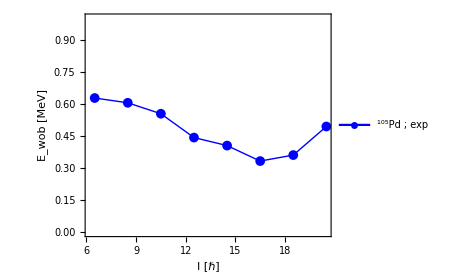

```mathematica
data=wobbling[yrastEn,wob1En,wob1Spin];
fig=ListPlot[data,PlotRange->{Automatic,{0,1}},Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,AspectRatio->0.8,PlotStyle->{Thick,Blue},FrameStyle->Directive[Thick,Black],FrameLabel->{"I [ℏ]","E_wob [MeV]"},LabelStyle->{18,Bold,Black},PlotLegends->Placed[{Row[{Superscript["","105"],"Pd ; exp"}]},{0.3,0.9}],ImageSize->350];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/experimental-data-collection-wobblers/105.pdf",fig];
Show[fig]
```